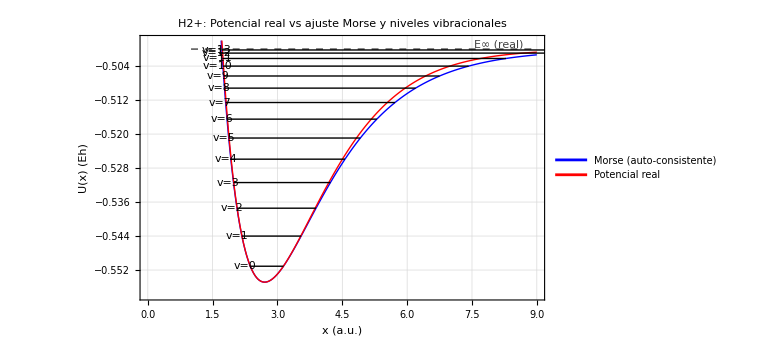

x_min real (a0) | 2.7036
E_min real (Eh) | -0.554849
E_inf real (Eh) | -0.500000
D_e = E_inf - E_min (Eh) | 0.054849
a (a0^-1) (por curvatura) | 0.697385
ω_e (Eh) | 0.007623
v_max teórico (Morse) | 13
Δ_asíntota (Morse - Real) (Eh) | 0.000000
B_e (a.u.) | 0.00007452

Nivel | E_rel (Eh) | E_abs (Eh)
v=0 | 0.003745 | -0.551103
v=1 | 0.010839 | -0.544010
v=2 | 0.017403 | -0.537446
v=3 | 0.023437 | -0.531412
v=4 | 0.028941 | -0.525907
v=5 | 0.033916 | -0.520933
v=6 | 0.038360 | -0.516488
v=7 | 0.042275 | -0.512573
v=8 | 0.045660 | -0.509188
v=9 | 0.048516 | -0.506333
v=10 | 0.050841 | -0.504007
v=11 | 0.052637 | -0.502212
v=12 | 0.053903 | -0.500946
v=13 | 0.054639 | -0.500210

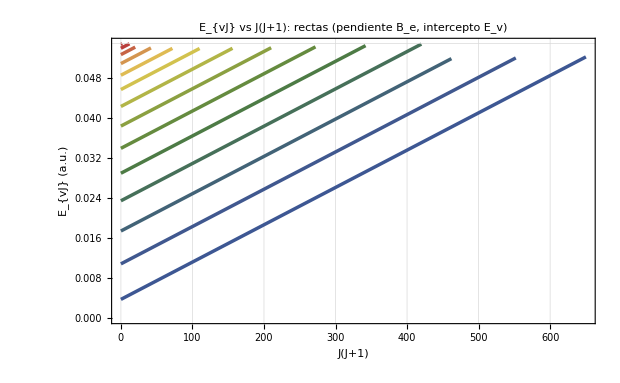

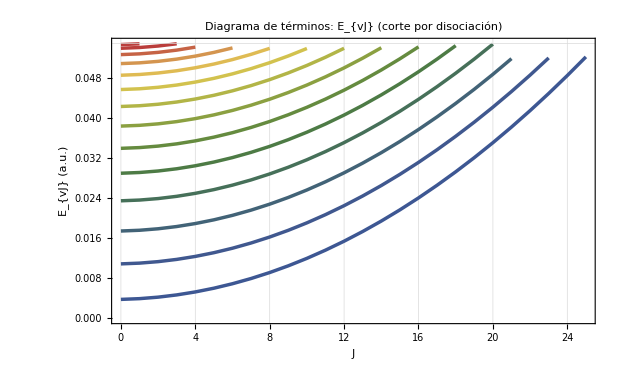

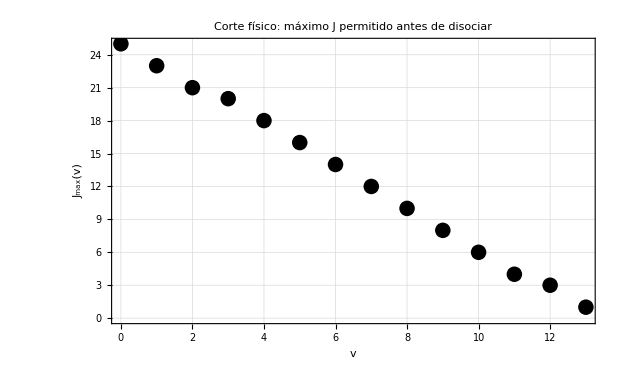

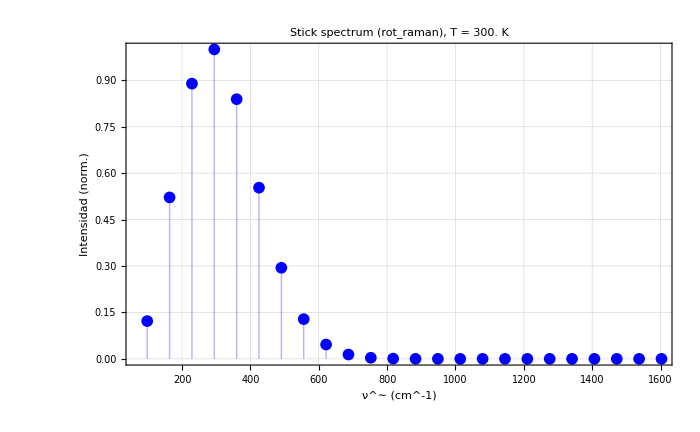

```mathematica
(* =========================================================
WL–VR–03 Pipeline unificado:Potencial real Ex(x)->ajuste Morse->constantes (De,a,ωe,Be)->niveles Ev->términos EvJ+Jmax(v)->stick spectrum (cm^-1)=========================================================*)ClearAll["Global`*"];

(*-------------------------A) Parámetros de entrada/control-------------------------*)
Za=1;C1=1;

mu=918.0;    (*a.u.*)
hbar=1.0;

xDomain={1.0,9.0};   (*búsqueda del mínimo real*)
xInfinity=80.0;         (*aproximación de asíntota*)

(*¿usar energía absoluta (Eh) o relativa al mínimo?*)
useAbsoluteEnergy=False;  (*True:E_abs,umbral=EinfReal;False:E_rel,umbral=De*)

(*límites de gráfica*)
vPlotMax=13;     (*cuántos v dibujar en potencial con niveles*)
vTermMax=13;     (*cuántos v dibujar en term diagrams*)
Jcap=400;    (*tope de búsqueda para Jmax(v)*)

(*stick spectrum:elige modo*)
stickMode="rot_raman";
(*"rot_dipole":rotacional dipolar (pedagógico) ΔJ=+1 en v=0 "rovib_dipole":rovibracional dipolar (pedagógico) v=0->1,ΔJ=±1 "rot_raman":rotacional Raman ΔJ=+2 en v=0 (más fiel a H2+)*)

Tkelvin=300.0;         (*para intensidades tipo Boltzmann si quieres*)
useIntensity=True;

(*conversiones*)
EhToCm1=219474.63067;
kBEhK=3.166811563*10^-6;  (*kB en Eh/K*)

(*estética*)
gridStyle=Directive[GrayLevel[.88],Dashed];
asymStyle=Directive[GrayLevel[.25],Dashed,Thick];
morseStyle={Thick,Blue};
realStyle={Thick,Red};
levelStyle={Black,Dashed};
arrowStyle={Blue,AbsoluteThickness[2]};
arrowHeadSz=0.025;

(*-------------------------B) Potencial real Ex(x) (TU FUNCIÓN)-------------------------*)
Ex[x_,Za_,C1_]:=(E^-x Za^2 (6 (1+C1^2) (1+x)-3 (1+C1^2) E^(2 x) (2+x-2 Za)-2 C1 E^x (3+9 x+9 x^2+x^3-2 (6+x (3+x)) Za)))/(2 x (3 (1+C1^2) E^x+2 C1 (3+x (3+x))));

(*-------------------------C) Mínimo y asíntota del potencial real-------------------------*)
xMinReal=x/. Last@NMinimize[{Ex[x,Za,C1],xDomain[[1]]<x<xDomain[[2]]},x];
EminReal=N@Ex[xMinReal,Za,C1];
EinfReal=N@Ex[xInfinity,Za,C1];

DeReal=EinfReal-EminReal;  (*profundidad real*)
kReal=N[D[Ex[x,Za,C1],{x,2}]/. x->xMinReal];

If[DeReal<=0||kReal<=0,Print["ERROR: DeReal o kReal no positivos. Revisa dominio/minimización."];
Abort[];];

(*Morse auto-consistente:U_M=Emin+De(1-exp(-a(x-Re)))^2*)
RE=xMinReal;
De=DeReal;
aM=Sqrt[kReal/(2 De)];
offset=EminReal;

MorseV[x_]:=offset+De (1-Exp[-aM (x-RE)])^2;

(*frecuencia Morse (a.u.)*)
omegaE=aM Sqrt[(2 De)/mu];

(*energía vibracional (relativa al mínimo)*)
EvibRel[v_?NonNegative]:=omegaE (v+1/2)-(omegaE^2 (v+1/2)^2)/(4 De);

(*v_max teórico*)
vMax=Floor[(2 De)/omegaE-1/2];

(*-------------------------D) Rotación y términos rovibracionales-------------------------*)
Be=1/(2 mu RE^2);

Erot[J_?NonNegative]:=Be J (J+1);

Erel[v_?NonNegative,J_?NonNegative]:=EvibRel[v]+Erot[J];
Eabs[v_?NonNegative,J_?NonNegative]:=EminReal+Erel[v,J];

Eplot[v_,J_]:=If[useAbsoluteEnergy,Eabs[v,J],Erel[v,J]];
Ethreshold:=If[useAbsoluteEnergy,EinfReal,De];

(*Jmax(v) por criterio energético (corte)*)
Jmax[v_?NonNegative]:=Module[{js},js=Select[Range[0,Jcap],Eplot[v,#]<Ethreshold&];
If[js==={},-1,Max[js]]];

(*turning points del Morse (para dibujar niveles en el pozo)*)
turningPoints[v_?NonNegative]:=Module[{Elevel,sols},Elevel=offset+EvibRel[v];
sols=x/. NSolve[MorseV[x]==Elevel&&x>0,x,Reals];
sols=Select[sols,NumericQ];
If[Length[sols]>=2,{Min[sols],Max[sols]},{}]];

(*-------------------------E) Fig 1:potencial real vs Morse+niveles+línea de asíntota-------------------------*)
xRangePlot={xDomain[[1]],xDomain[[2]]};
yRangePlot={offset-0.003,offset+De+0.002};

basePlot=Plot[{MorseV[x],Ex[x,Za,C1]},{x,Sequence@@xRangePlot},PlotStyle->{morseStyle,realStyle},PlotRange->{yRangePlot},Frame->True,FrameLabel->{"x (a.u.)","U(x) (Eh)"},PlotLegends->{"Morse","Potencial real"},GridLines->Automatic,GridLinesStyle->gridStyle,PlotPoints->250,ImageSize->Large,PlotLabel->"H2+: Potencial real vs ajuste Morse y niveles vibracionales"];

asymptoteG=Graphics[{asymStyle,Line[{{xRangePlot[[1]],EinfReal},{xRangePlot[[2]],EinfReal}}],Text[Style["E∞ (real)",11,GrayLevel[.25]],{xRangePlot[[2]]-0.3,EinfReal},{1,-1}]}];

levelsG=Graphics@Table[Module[{tp=turningPoints[v],Elevel=offset+EvibRel[v]},If[tp==={},Nothing,{levelStyle,Line[{{tp[[1]],Elevel},{tp[[2]],Elevel}}],Text[Style["v="<>ToString[v],11],{tp[[1]]-0.12,Elevel},{1,0}]}]],{v,0,Min[vPlotMax,vMax]}];

Show[basePlot,asymptoteG,levelsG]

(*-------------------------F) Tabla 1:parámetros-------------------------*)
deltaAsym=(offset+De)-EinfReal;  (* ~0 por construcción*)

paramTable=Grid[{{"x_min real (a0)",NumberForm[xMinReal,{7,4}]},{"E_min real (Eh)",NumberForm[EminReal,{10,6}]},{"E_inf real (Eh)",NumberForm[EinfReal,{10,6}]},{"D_e = E_inf - E_min (Eh)",NumberForm[De,{10,6}]},{"a (a0^-1) (por curvatura)",NumberForm[aM,{10,6}]},{"ω_e (Eh)",NumberForm[omegaE,{10,6}]},{"v_max teórico (Morse)",vMax},{"Δ_asíntota (Morse - Real) (Eh)",NumberForm[deltaAsym,{10,6}]},{"B_e (a.u.)",NumberForm[Be,{10,8}]}},Frame->All,Spacings->{2,1},ItemStyle->12];

paramTable

(*-------------------------G) Tabla 2:niveles vibracionales-------------------------*)
energyTable=Table[{"v="<>ToString[v],NumberForm[EvibRel[v],{10,6}],NumberForm[EminReal+EvibRel[v],{10,6}]},{v,0,vMax}];

TableForm[energyTable,TableHeadings->{None,{"Nivel","E_rel (Eh)","E_abs (Eh)"}}]

(*-------------------------H) Term diagrams+Jmax(v)-------------------------*)
vList=Range[0,Min[vTermMax,vMax]];
stylesV=Table[Directive[Thickness[0.004],ColorData["DarkRainbow"][Rescale[v,{0,vMax}]]],{v,vList}];
vLegend=Placed[LineLegend[stylesV,("v="<>ToString/@vList)],Right];

termDataJ[v_]:=Table[{J,Eplot[v,J]},{J,0,Max[0,Jmax[v]]}];
termDataJJ[v_]:=Table[{J (J+1),Eplot[v,J]},{J,0,Max[0,Jmax[v]]}];

termPlotJJ=ListLinePlot[termDataJJ/@vList,PlotStyle->stylesV,Frame->True,FrameLabel->{"J(J+1)",If[useAbsoluteEnergy,"E_{vJ} (Eh)","E_{vJ} (a.u.)"]},GridLines->{Automatic,{Ethreshold}},GridLinesStyle->{gridStyle,Directive[GrayLevel[.35],Thick,Dashed]},PlotRange->All,ImageSize->620,PlotLabel->"E_{vJ} vs J(J+1): rectas (pendiente B_e, intercepto E_v)",PlotLegends->vLegend
];

termPlotJ=ListLinePlot[termDataJ/@vList,PlotStyle->stylesV,Frame->True,FrameLabel->{"J",If[useAbsoluteEnergy,"E_{vJ} (Eh)","E_{vJ} (a.u.)"]},GridLines->{Automatic,{Ethreshold}},GridLinesStyle->{gridStyle,Directive[GrayLevel[.35],Thick,Dashed]},PlotRange->All,ImageSize->620,PlotLabel->"Diagrama de términos: E_{vJ} (corte por disociación)",PlotLegends->vLegend
];

jmaxPlot=ListPlot[Table[{v,Jmax[v]},{v,vList}],PlotStyle->{Black,PointSize[0.018]},Frame->True,FrameLabel->{"v","J_max(v)"},GridLines->{Automatic,Automatic},GridLinesStyle->gridStyle,ImageSize->620,PlotLabel->"Corte físico: máximo J permitido antes de disociar"];

termPlotJJ
termPlotJ
jmaxPlot

(*-------------------------I) Stick spectrum (cm^-1)-------------------------*)
ErotAbs[J_]:=Be J (J+1);  (*en Eh;es independiente de usar absolute/relative*)

boltz[J_]:=Exp[-ErotAbs[J]/(kBEhK Tkelvin)];  (*población~exp(-E/kT)*)

(*Intensidad modelo (pedagógica):rot_dipole:I∝(2J+1)(J+1) exp(-EJ/kT) rot_raman:I∝(2J+1)(2J+3) exp(-EJ/kT) (forma simple) rovib_dipole:I∝(2J+1) exp(-EJ/kT) (simplificado)*)
IrotDip[J_]:=(2 J+1) (J+1) boltz[J];
IrotRam[J_]:=(2 J+1) (2 J+3) boltz[J];
Irovib[J_]:=(2 J+1) boltz[J];

lines=Which[stickMode=="rot_dipole",Table[With[{dE=ErotAbs[J+1]-ErotAbs[J],inten=IrotDip[J]},{dE*EhToCm1,If[useIntensity,inten,1.0]}],{J,0,Max[2,Jmax[0]-1]}],stickMode=="rot_raman",Table[With[{dE=ErotAbs[J+2]-ErotAbs[J],inten=IrotRam[J]},{dE*EhToCm1,If[useIntensity,inten,1.0]}],{J,0,Max[2,Jmax[0]-2]}],stickMode=="rovib_dipole",Table[With[{dE=(EvibRel[1]-EvibRel[0])+(ErotAbs[J+1]-ErotAbs[J]),inten=Irovib[J]},{dE*EhToCm1,If[useIntensity,inten,1.0]}],{J,0,Max[2,Jmax[0]-1]}],True,{}];

(*normaliza intensidades a 1*)
If[useIntensity&&lines=!={},lines=lines/. {x_,y_}:>{x,y/Max[lines[[All,2]]]}];

stickPlot=ListPlot[lines,PlotStyle->{Blue,PointSize[0.012]},Filling->Axis,Frame->True,FrameLabel->{"\!\(\*OverscriptBox[\(ν\), \(∼\)]\) (cm^-1)","Intensidad (norm.)"},GridLines->{Automatic,Automatic},GridLinesStyle->gridStyle,ImageSize->700,PlotRange->All,PlotLabel->Row[{"Stick spectrum (",stickMode,"),  T = ",Tkelvin," K  ",If[stickMode=="rot_dipole"||stickMode=="rovib_dipole","(nota: H2+ real: Raman/cuadrupolar)",""]}]];

stickPlot

(*-------------------------J) (Opcional) export-------------------------*)
Export["WL-VR-03_paramTable.png",paramTable,ImageResolution->300];
Export["WL-VR-03_termJJ.pdf",termPlotJJ];
Export["WL-VR-03_sticks.pdf",stickPlot];
```